```mathematica
n=2;
myFn[θ_]=Exp[ⅈ θ n]+Exp[-ⅈ θ n];
```

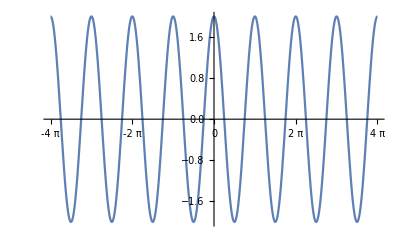

```mathematica
Plot[myFn[p],{p,-4π,4Pi},Ticks->{Range[-4Pi,4Pi,Pi],Automatic}]
```

```mathematica
Kern1D[x_,xp_,ξ_]=Sqrt[ⅈ/(2 Pi*Sin[ξ])]*Exp[-ⅈ/2((xp^2+x^2)/Tan[ξ]-(2*xp*x)/Sin[ξ])];
D1[x_,xp_,y_,yp_,ξ_]=Kern1D[x,xp,ξ]Kern1D[y,yp,ξ];
D2[x_,xp_,y_,yp_,ξ_]=1/2(Kern1D[x,xp,ξ]Kern1D[y,yp,ξ]+Kern1D[-x,xp,ξ]Kern1D[-y,yp,ξ]);
D3[x_,xp_,y_,yp_,ξ_]=ⅈ/(4Pi Sin[ξ])Exp[-ⅈ/2 (x^2+xp^2+y^2+yp^2)/Tan[ξ]](Exp[-ⅈ/Sin[ξ](x*xp+y*yp)]+Exp[ⅈ/Sin[ξ](x*xp+y*yp)])
```

(ⅈ ⅇ^(-1/2 ⅈ (x^2+xp^2+y^2+yp^2) Cot[ξ]) (ⅇ^(-ⅈ (x xp+y yp) Csc[ξ])+ⅇ^(ⅈ (x xp+y yp) Csc[ξ])) Csc[ξ])/(4 π)

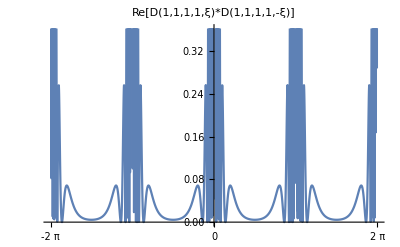

periodicityKernels.pdf

```mathematica
pl1=Plot[Re[D3[1,1,1,1,p]*D3[1,1,1,1,-p]],{p,-2Pi,2Pi},Ticks->{Range[-4Pi,4Pi,Pi],Automatic},PlotLabel->"Re[D(1,1,1,1,ξ)*D(1,1,1,1,-ξ)]"]
Export["periodicityKernels.pdf",pl1]
```

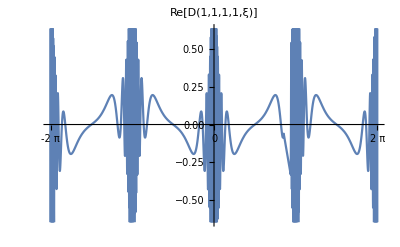

periodicityKernel.pdf

```mathematica
pl2=Plot[Re[D3[1,1,1,1,p]],{p,-2Pi,2Pi},Ticks->{Range[-4Pi,4Pi,Pi],Automatic},PlotLabel->"Re[D(1,1,1,1,ξ)]"]
Export["periodicityKernel.pdf",pl2]
```

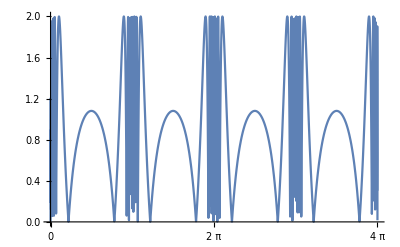

```mathematica
Plot[Abs[Exp[ⅈ/Sin[x]]+Exp[-ⅈ/Sin[x]]],{x,0,4Pi},Ticks->{Range[-4Pi,4Pi,Pi],Automatic}]
```

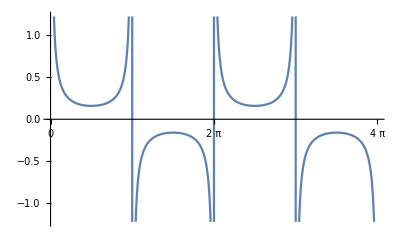

```mathematica
Plot[1/(2*Pi*Sin[x]),{x,0,4Pi},Ticks->{Range[-4Pi,4Pi,Pi],Automatic}]
```

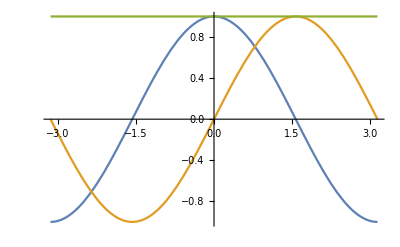

```mathematica
Plot[{Re[Exp[ⅈ x]],Im[Exp[ⅈ x]],Abs[Exp[ⅈ x]]},{x,-Pi,Pi}]
```